## Task 12.6.

“Slicing” by planes x=const

```mathematica
a=2;
b=3;
c=4;
Show[
RegionPlot3D[x/a+y/b+z/c<=1&&x>=0&&y>=0&&z>=0,{x,0,2},{y,0,3},{z,0,4},PlotStyle->Directive[Blue,Opacity[0.5]],Mesh->None,PlotTheme->"Classic",AxesLabel->{"x","y","z"},LabelStyle->"Subsection"],
ContourPlot3D[x==1.0,{x,0,5},{y,0,5},{z,0,5},ContourStyle->Directive[Green,Opacity[0.8],Specularity[White,30]]]
]
```

-Graphics3D-

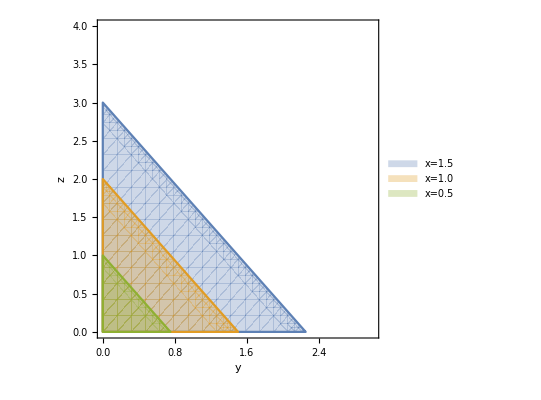

```mathematica
t=1.0;
Show[
RegionPlot[{y/b+z/c<=1.0-(0.5t)/a&&y>=0&&z>=0,y/b+z/c<=1.0-t/a&&y>=0&&z>=0,y/b+z/c<=1.0-(1.5t)/a&&y>=0&&z>=0},{y,0,3},{z,0,4},AxesLabel->{"y","z"},PlotLegends->{"x=1.5","x=1.0","x=0.5"},BoundaryStyle->Thick]
]
```

“Slicing” by planes y=const

```mathematica
a=2;
b=3;
c=4;
Show[
RegionPlot3D[x/a+y/b+z/c<=1&&x>=0&&y>=0&&z>=0,{x,0,2},{y,0,3},{z,0,4},PlotStyle->Directive[Blue,Opacity[0.5]],Mesh->None,PlotTheme->"Classic",AxesLabel->{"x","y","z"},LabelStyle->"Subsection"],
ContourPlot3D[y==1.0,{x,0,5},{y,0,5},{z,0,5},ContourStyle->Directive[Green,Opacity[0.8],Specularity[White,30]]]
]
```

-Graphics3D-

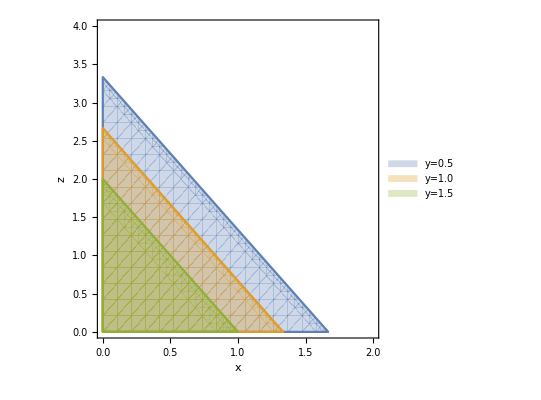

```mathematica
t=1;
Show[
RegionPlot[{x/a+z/c<=1.0-(0.5t)/b&&x>=0&&z>=0,x/a+z/c<=1.0-t/b&&x>=0&&z>=0,x/a+z/c<=1.0-(1.5t)/b&&x>=0&&z>=0},{x,0,2},{z,0,4},AxesLabel->{"x","z"},PlotLegends->{"y=0.5","y=1.0","y=1.5"},BoundaryStyle->Thick]
]
```

## Task 13.3.

```mathematica
a=2;
b=3;
c=4;
Show[
RegionPlot3D[y+z<=3&&x>=0&&x<=2&&y>=0&&z>=0,{x,0,2},{y,0,3},{z,0,3},PlotStyle->Directive[Blue,Opacity[0.5]],Mesh->None,PlotTheme->"Classic",AxesLabel->{"x","y","z"},LabelStyle->"Subsection"],
ContourPlot3D[x==1.0,{x,0,2},{y,0,8},{z,-4,4},Mesh->None,ContourStyle->Directive[Green,Opacity[0.8],Specularity[White,30]]]
]
```

-Graphics3D-

```mathematica
t=1;
Show[
RegionPlot[{x/a+z/c<=1.0-(0.5t)/b&&x>=0&&z>=0,x/a+z/c<=1.0-t/b&&x>=0&&z>=0,x/a+z/c<=1.0-(1.5t)/b&&x>=0&&z>=0},{x,0,2},{z,0,4},AxesLabel->{"x","z"},PlotLegends->{"y=0.5","y=1.0","y=1.5"},BoundaryStyle->Thick]
]
```

## Task 12.9.

“Slicing” by planes x=const

```mathematica
Show[
RegionPlot3D[x>=0&&y>=0&&z>=0&&x<=1&&y<=(1-x^2)^(1/2)&&z<=x^2+y^2,{x,0,1},{y,0,1},{z,0,0.8},PlotStyle->Directive[Blue,Opacity[0.5]],Mesh->None,PlotTheme->"Classic",AxesLabel->{"x","y","z"},LabelStyle->"Subsection"],
ContourPlot3D[x==0.5,{x,0,5},{y,0,5},{z,0,5},ContourStyle->Directive[Green,Opacity[0.8],Specularity[White,30]]]
]
```

-Graphics3D-

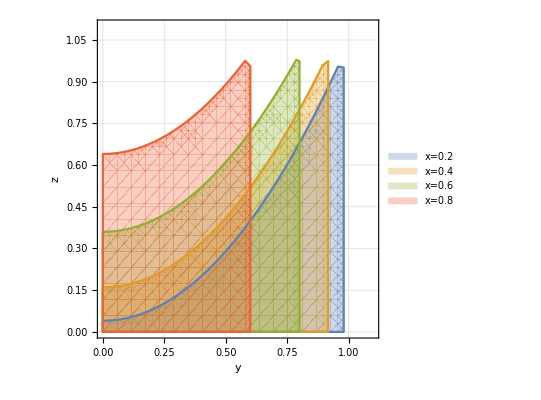

```mathematica
t1=0.2;
t2=0.4;
t3=0.6;
t4=0.8;
Show[
RegionPlot[{y>=0&&z>=0&&y<=(1-t1^2)^(1/2)&&z<=t1^2+y^2,y>=0&&z>=0&&y<=(1-t2^2)^(1/2)&&z<=t2^2+y^2,y>=0&&z>=0&&y<=(1-t3^2)^(1/2)&&z<=t3^2+y^2,y>=0&&z>=0&&y<=(1-t4^2)^(1/2)&&z<=t4^2+y^2},{y,0,1.1},{z,0,1.1},AxesLabel->{"y","z"},PlotLegends->{"x=0.2","x=0.4","x=0.6","x=0.8"},BoundaryStyle->Thick,PlotTheme->"Detailed"]
]
```

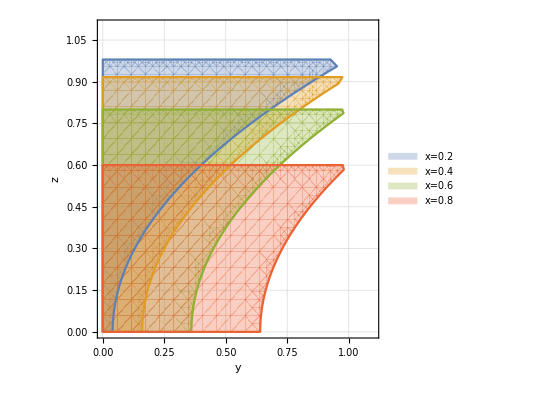

```mathematica
t1=0.2;
t2=0.4;
t3=0.6;
t4=0.8;
Show[
RegionPlot[{y>=0&&z>=0&&y<=(1-t1^2)^(1/2)&&z<=t1^2+y^2,y>=0&&z>=0&&y<=(1-t2^2)^(1/2)&&z<=t2^2+y^2,y>=0&&z>=0&&y<=(1-t3^2)^(1/2)&&z<=t3^2+y^2,y>=0&&z>=0&&y<=(1-t4^2)^(1/2)&&z<=t4^2+y^2},{z,0,1.1},{y,0,1.1},AxesLabel->{"y","z"},PlotLegends->{"x=0.2","x=0.4","x=0.6","x=0.8"},BoundaryStyle->Thick,PlotTheme->"Detailed"]
]
```

“Slicing” by planes y=const

```mathematica
Show[
RegionPlot3D[x>=0&&y>=0&&z>=0&&x<=1&&y<=(1-x^2)^(1/2)&&z<=x^2+y^2,{x,0,1},{y,0,1},{z,0,0.8},PlotStyle->Directive[Blue,Opacity[0.5]],Mesh->None,PlotTheme->"Classic",AxesLabel->{"x","y","z"},LabelStyle->"Subsection"],
ContourPlot3D[z==0.5,{x,0,5},{y,0,5},{z,0,5},ContourStyle->Directive[Green,Opacity[0.8],Specularity[White,30]]]
]
```

-Graphics3D-

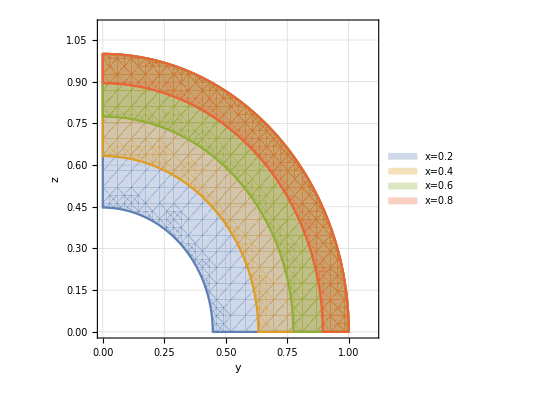

```mathematica
t1=0.2;
t2=0.4;
t3=0.6;
t4=0.8;
Show[
RegionPlot[{x>=0&&y>=0&&x<=1&&y<=(1-x^2)^(1/2)&&t1<=x^2+y^2,x>=0&&y>=0&&x<=1&&y<=(1-x^2)^(1/2)&&t2<=x^2+y^2,x>=0&&y>=0&&x<=1&&y<=(1-x^2)^(1/2)&&t3<=x^2+y^2,x>=0&&y>=0&&x<=1&&y<=(1-x^2)^(1/2)&&t4<=x^2+y^2},{x,0,1.1},{y,0,1.1},AxesLabel->{"y","z"},PlotLegends->{"x=0.2","x=0.4","x=0.6","x=0.8"},BoundaryStyle->Thick,PlotTheme->"Detailed"]
]
```